```mathematica
A=10006.6
```

10006.6

```mathematica
V=998785
```

998785

```mathematica
n=10000
```

10000

```mathematica
k=5
```

5

```mathematica
Di=1
```

1

```mathematica
h=k/Di
```

5

```mathematica
LogPlot[(n*A*h*Di)/V*Exp[h^2*Di*t]*Erfc[h*Sqrt[Di*t]],{t,0,200}PlotRange-> {{0,200},{0,20}}]
```

LogPlot::pllim: Range specification {t, 0, 200}\ PlotRange → {{0, 200}, {0, 20}} is not of the form {x, xmin, xmax}.

LogPlot[((n A h Di) Exp[h^2 Di t] Erfc[h √(Di t)])/V,{t,0,200} PlotRange→{{0,200},{0,20}}]

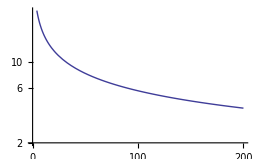

```mathematica
LogPlot[((n A h Di) Exp[h^2 Di t] Erfc[h √(Di t)])/V,{t,0,200}, PlotRange->{{0,200},{2,28}},Ticks->{{0,50,100,150,200},{2,4,6,8,10}}]
```

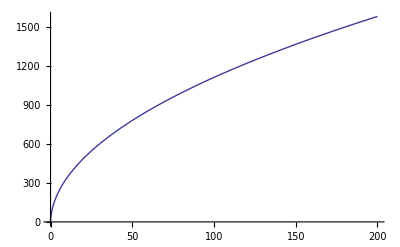

```mathematica
Plot[(n A)/(h V)(Exp[h^2 Di t] Erfc[h √(Di t)]-1+2/(√π)h √(Di t)),{t,0,200}]
```

```mathematica
plot = Plot[(n A)/(h V)(Exp[h^2 Di t] Erfc[h √(Di t)]-1+2/(√π)h √(Di t)),{t,0,200}]
```

-Graphics-

```mathematica
mydata=Flatten[Cases[plot,Line[x__]->x,Infinity],1]
```

{{4.08163×10^-6,0.00202921},{0.0613436,15.3814},{0.122683,25.2661},{0.184023,33.2825},{0.245362,40.2196},{0.306702,46.4267},{0.368041,52.0964},{0.49072,62.265},{0.55206,66.9022},{0.613399,71.3035},{0.736078,79.5224},{0.981436,94.1963},{1.04278,97.5787},{1.10412,100.866},{1.22679,107.187},{1.47215,118.967},{1.96287,139.946},{2.02421,142.378},{2.08555,144.773},{2.20823,149.464},{2.45358,158.475},{2.9443,175.253},{3.92573,205.089},{3.99223,206.968},{4.05873,208.833},{4.19173,212.516},{4.45772,219.714},{4.98972,233.497},{6.0537,259.029},{6.1202,260.548},{6.1867,262.058},{6.3197,265.055},{6.58569,270.956},{7.11769,282.413},{8.18167,304.114},{8.24376,305.336},{8.30586,306.553},{8.43004,308.974},{8.67841,313.763},{9.17515,323.141},{10.1686,341.166},{12.1556,374.756},{16.0515,433.453},{20.2777,489.536},{24.2218,536.803},{28.4962,583.866},{32.6926,626.747},{36.6069,664.328},{40.8515,702.875},{44.814,737.092},{48.6986,769.197},{52.9134,802.615},{56.8461,832.616},{61.1091,863.988},{65.2941,893.738},{69.1971,920.636},{73.4303,948.966},{77.3815,974.681},{81.6628,1001.81},{85.8662,1027.77},{89.7876,1051.42},{94.0392,1076.48},{98.0088,1099.38},{101.9,1121.38},{106.122,1144.77},{110.062,1166.19},{114.332,1188.97},{118.524,1210.93},{122.434,1231.06},{126.674,1252.53},{130.632,1272.26},{134.513,1291.3},{138.723,1311.66},{142.652,1330.38},{146.91,1350.39},{150.887,1368.8},{154.785,1386.63},{159.014,1405.71},{162.961,1423.29},{167.238,1442.1},{171.437,1460.34},{175.354,1477.15},{179.601,1495.17},{183.567,1511.8},{187.454,1527.93},{191.671,1545.25},{195.607,1561.23},{195.676,1561.51},{195.744,1561.79},{195.881,1562.34},{196.156,1563.45},{196.705,1565.66},{197.803,1570.08},{197.872,1570.36},{197.941,1570.64},{198.078,1571.19},{198.353,1572.29},{198.902,1574.49},{198.97,1574.77},{199.039,1575.04},{199.176,1575.59},{199.451,1576.69},{199.519,1576.97},{199.588,1577.24},{199.725,1577.79},{199.794,1578.06},{199.863,1578.34},{199.931,1578.61},{200.,1578.89}}

```mathematica
Export["/Users/satya/Desktop/off_lattice.csv",mydata,"CSV"];
```